```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"CMU Serif"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<CustomTicks`
```

Get::noopen: Cannot open CustomTicks`.

$Failed

```mathematica
pp11 = Import["pp11_partonic.dat","List"];
ppm1m1 = Import["ppm1m1_partonic.dat","List"];
pp1m1 = Import["pp1m1_partonic.dat","List"];
ppm11 = Import["ppm11_partonic.dat","List"];
sqrtsList=Table[350+25*i,{i,0,400}];
```

```mathematica
ppm1m1 ;
```

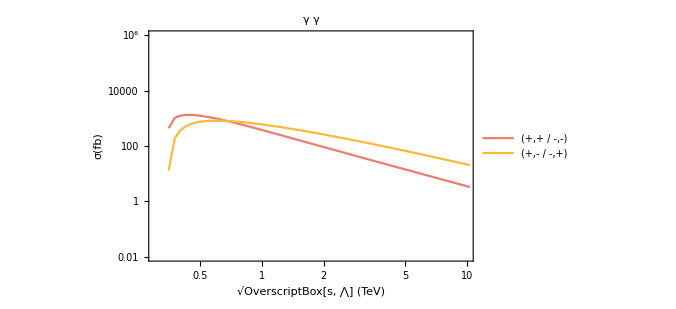

```mathematica
factor=0.3894*10^12;
lineplot=ListLogLogPlot[{
Transpose[{sqrtsList/10^3,factor*pp11}],
Transpose[{sqrtsList/10^3,factor*pp1m1}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9]},Frame->True,FrameLabel->{Style["\!\(\*SqrtBox[\(s^⋀\)]\) (TeV)",Black,17,FontFamily->"Times"],Style["σ(fb)",Black,18,FontFamily->"Times"]},
PlotLabel->Style["γ γ",Black,17,FontFamily->"Times"],
PlotLegends->Placed[{Style[" (+,+ / -,-) ",Black,15,FontFamily->"Times"],Style[" (+,- / -,+)  ",Black,15,FontFamily->"Times"]},{{0.15,0.14},{0.25,0.3}}],
PlotRange->{{.300,10},{0.01,1000000}},FrameTicks->{{ticks1,Automatic},{{0.5,1,2,5,10},Automatic}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
(*customticks package*)
```

```mathematica
ticks0=LogTicks[10,-2,6,TickLabelStep->2];
ticks1=ticks0;
Do[ticks1[[i,1]]=10^(ticks0[[i,1]]),{i,1,Length[ticks0]}]
ticks1;
```

```mathematica
Export["PP_partonic.pdf",lineplot]
```

PP_partonic.pdf